```mathematica
<<EcoEvo`
```

EcoEvo Package Version 0.9.10 (June 29, 2019)
Christopher A. Klausmeier <christopher.klausmeier@gmail.com>

```mathematica
SetModel[{
Pop[n1]->{Variable->n1,Equation:> n1[t]*(r1 -(n1[t]+α12 n2[t])/k1)+i1-m1 n1[t]},
Pop[n2]->{Variable->n2,Equation:> n2[t]*(r2 -(n2[t]+α21 n1[t])/k2)+i2-m2 n2[t]}
}]
```

## setup

```mathematica
SetDirectory["/Users/klaus/Work/research/current/2018 reus/fortran"]
```

/Users/klaus/Work/research/current/2018 reus/fortran

```mathematica
tend:=Floor[tmax/tskip]
```

```mathematica
WriteList[strm_,list_List]:=Module[{},Do[Write[strm,list[[i]]//FortranForm],{i,1,Length[list]}]];
```

```mathematica
RunSim:=Module[{stream,tmp},
stream=OpenWrite["input"];
WriteList[stream,{r1,r2,k1,k2,α12,α21,i1,i2,m1,m2,e}];
WriteList[stream,{n1max,n2max,tskip,tmax}];
WriteList[stream,{rtol,atol,mf,ml,mu}];
Do[
Do[
Write[stream,pinit[n1,n2]];
,{n1,0,n1max}]
,{n2,0,n2max}];
Close[stream];
Clear[stream];

Run["rm output"];

PrintTemporary["running simulation..."];

Print["time=",AbsoluteTiming[Run["./mc21<input"]][[1]]," s"];

PrintTemporary["reading data..."];

tmp=ReadList["!grep -v 't=' output",Number];

PrintTemporary["refurbishing data..."];

pdat=ArrayReshape[tmp,{tend+1,n1max+1,n2max+1}];

slist=ReadList["!cut -b18-25 messages",Number];

(*Clear[dat];*)

];
```

```mathematica
ArchiveSim[notes_]:=Module[{stream,datestamp},
datestamp=ToString[Round[FromDate[Date[]]]];
Run["compress < input > input_"<>datestamp<>".Z"];
Run["compress < output > output_"<>datestamp<>".Z"];
Run["compress < messages > messages_"<>datestamp<>".Z"];
stream=OpenAppend["archives.txt"];
WriteString[stream,datestamp<>" "<>notes<>"\n"];
Close[stream];Clear[stream];
];
```

```mathematica
p[n1_Integer,n2_Integer][t_Integer]:=pdat⟦t+1,n2+1,n1+1⟧
```

```mathematica
p0[t_Integer]:=pdat⟦t+1,1,1⟧;
p1[t_Integer]:=Total[pdat⟦t+1,1,2;;⟧];
p2[t_Integer]:=Total[pdat⟦t+1,2;;,1⟧];
p12[t_Integer]:=Total[Flatten[pdat⟦t+1,2;;,2;;⟧]];
ptot[t_Integer]:=Total[Flatten[pdat⟦t+1,All,All⟧]];
```

## simulations

```mathematica
mf=25; (* method *)
ml:=n1max+1; (* # lower bands *)
mu:=n1max+1; (* # upper bands *)
rtol=0;
atol=10^-7;

n1max=100;
n2max=100;

r1=1.0;
k1=50;
α12=0.8;
m1=0.01;

r2=1.0;
k2=50;
α21=0.8;
m2=0.01;

e=0.0;
i1=i2=0.0;

tmax=1000.0;
tskip=10.0;
```

```mathematica
SolveEcoEq[]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{{n1→0,n2→0},{n1→49.5,n2→0},{n1→0,n2→49.5},{n1→27.5,n2→27.5}}

```mathematica
(* near coex point *)
pinit[n1_,n2_]:=If[n1==25&&n2==25,1.0,0.0];
(* invasion *)
(*pinit[n1_,n2_]:=Which[
n1==0&&n2==50,0.01,
n1==50&&n2==0,0.99,
True,0.0];*)
(*pinit[n1_,n2_]:=1./(n1max+1)(n2max+1)*)
```

```mathematica
RunSim
```

time=3.36044 s

```mathematica
{p0[tend],p1[tend],p2[tend],p12[tend]}
```

{0.,0.038572,0.0385705,0.923792}

```mathematica
ptot[tend]
```

1.00093

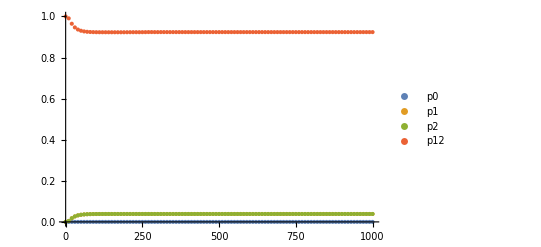

```mathematica
ListPlot[{
Table[{t*tskip,p0[t]},{t,0,tend}],
Table[{t*tskip,p1[t]},{t,0,tend}],
Table[{t*tskip,p2[t]},{t,0,tend}],
Table[{t*tskip,p12[t]},{t,0,tend}]
},PlotRange->{0,All},PlotLegends->{p0,p1,p2,p12}]
```

```mathematica
ListPlot3D[Flatten[Table[{n1,n2,Sqrt@p[n1,n2][1]},{n1,0,n1max},{n2,0,n2max}],1],PlotRange->All,AxesLabel->{n1,n2,p}]
```

-Graphics3D-

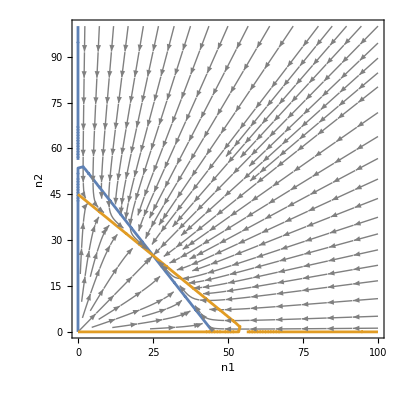

```mathematica
PlotEcoPhasePlane[{n1,0,n1max},{n2,0,n2max}]
```

```mathematica
pp=PlotEcoPhasePlane[{n1,0,n1max},{n2,0,n2max},Axes->False,PlotRangePadding->0,Frame->False];
lvl=-10^-6;
Show[
ListPlot3D[Flatten[Table[{n1,n2,p[n1,n2][tend]},{n1,0,n1max},{n2,0,n2max}],1],PlotRange->All,AxesLabel->{n1,n2,p},PlotStyle->Opacity[0.6],MeshFunctions->(Sqrt[#3]&)],
Graphics3D[{Texture[pp],EdgeForm[],Polygon[{{0,0,lvl},{n1max,0,lvl},{n1max,n2max,lvl},{0,n2max,lvl}},VertexTextureCoordinates->{{0,0},{1,0},{1,1},{0,1}}]},Lighting->"Neutral"],PlotLabel->tend*tskip
]
```

-Graphics3D-

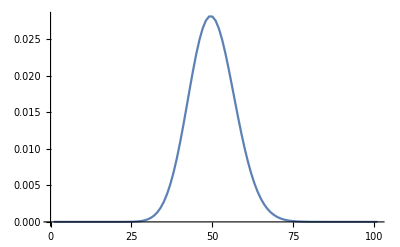

-Graphics-

```mathematica
ListLinePlot[Table[p[n1,0][tend],{n1,0,n1max}],PlotRange->All]
ListLinePlot[Table[p[0,n2][tend],{n2,0,n2max}],PlotRange->All]
```